## Vaja2 - rešitve

### Naloga 1

```mathematica
ClearAll[izraz, x]
izraz = (x^5-2x^2+3x+4)/(x^5-2x-1)
```

(4+3 x-2 x^2+x^5)/(-1-2 x+x^5)

```mathematica
izraz /. {x -> 1}
izraz /. {x -> 2}
izraz /. {x -> 3}
izraz /. {x -> 4}
```

-3

34/27

119/118

144/145

```mathematica
izraz /. x -> {1, 2, 3, 4}
```

{-3,34/27,119/118,144/145}

```mathematica
f[x_] := (x^5-2x^2+3x+4)/(x^5-2x-1)
```

```mathematica
f[1]
```

-3

```mathematica
f[2]
```

34/27

```mathematica
f[3]
```

119/118

```mathematica
f[4]
```

144/145

```mathematica
Table[f[x], {x, 1, 10}]
```

{-3,34/27,119/118,144/145,1547/1557,7726/7763,8367/8396,32668/32751,29459/29515,99834/99979}

```mathematica
Map[f, {1, 2, 3, 4}]
```

{f[1],f[2],f[3],f[4]}

### Naloga 2

```mathematica
sez = {10, 20, 30, 40, 50, 60, 70}
sez = Table[i, {i, 10, 70, 10}]
```

{10,20,30,40,50,60,70}

{10,20,30,40,50,60,70}

```mathematica
Take[sez, 3]
```

{10,20,30}

```mathematica
Take[sez, -2]
```

{60,70}

```mathematica
Take[sez, {2,4}]
```

{20,30,40}

```mathematica
Part[sez, {2, 3, 5}]
```

{20,30,50}

```mathematica
Drop[sez, {4,5}]
```

{10,20,30,60,70}

### Naloga 3

```mathematica
ClearAll[x, a]
sez = {x^6, x^2, a}
```

{x^6,x^2,a}

```mathematica
sez/. {x -> 3}
```

{729,9,a}

```mathematica
sez /. {x -> x^2}
```

{x^12,x^4,a}

```mathematica
sez /. {x^2 ->x }
```

{x^6,x,a}

```mathematica
sez /. {x -> {1, 2, 3}}
```

{{1,64,729},{1,4,9},a}

```mathematica
sez /. {x -> 3, a -> x}
```

{729,9,x}

```mathematica
sez //. {x -> 3, a -> x}
```

{729,9,3}

```mathematica
?ReplaceRepeated
```

expr//.rules repeatedly performs replacements until expr no longer changes.

```mathematica
Table[sez/.{x -> i}, {i, 1, 3}]
```

{{1,1,a},{64,4,a},{729,9,a}}

### Naloga 4

```mathematica
izraz1 = x^5 + 4x^3 + -9
odvod1 =D[izraz1, x]
```

-9+4 x^3+x^5

12 x^2+5 x^4

```mathematica
odvod1 /. {x -> 1}
odvod1 /. {x -> 5}
```

17

3425

```mathematica
izraz2 = E^(x^(1/4))
```

ⅇ^(x^(1/4))

```mathematica
odvod2 = D[izraz2, x]
```

(ⅇ^(x^(1/4)))/(4 x^(3/4))

```mathematica
odvod2 /. {x -> 1}
```

ⅇ/4

```mathematica
odvod2 /. {x -> 2}
```

(ⅇ^(2^(1/4)))/(4 2^(3/4))

```mathematica
izraz3 = Abs[x + 1]
```

Abs[1+x]

```mathematica
odvod3 = FullSimplify[D[izraz3, x], x ∈ Reals && x ≠ 0]
```

Sign[1+x]

```mathematica
odvod3 /. {x -> 1}
```

1

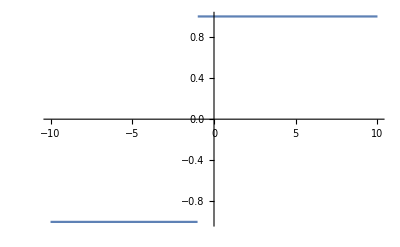

```mathematica
Plot[{odvod3}, {x, -10, 10}]
```

```mathematica
izraz3b = RealAbs[x + 1]
odvod3b = D[izraz3b, x]
odvod3b /. {x -> 1}
Plot[{odvod3b}, {x, -10, 10}]
```

RealAbs[1+x]

(1+x)/RealAbs[1+x]

1

-Graphics-

```mathematica
ClearAll[a, b, x]
izraz4 = a x^2+3b
```

3 b+a x^2

```mathematica
odvod4 = D[izraz4, x]
```

2 a x

### Naloga 5

```mathematica
f[x_] := x^3 Log[4x + 5]
```

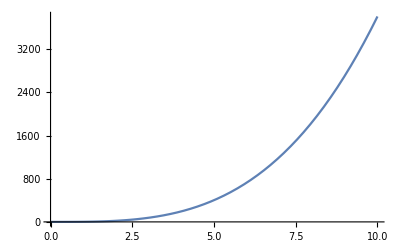

```mathematica
Plot[f[x], {x, 0, 10}]
```

5

20+75 Log[25]

-50 (2+5 Log[25])

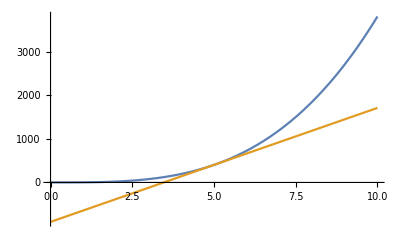

```mathematica
x0 = 5
k = D[f[x], x] /. {x -> x0}
n = n /.Solve[f[x0] == k*x0 + n, n] // First
Plot[{f[x], k*x + n}, {x, 0, 10}]
```

```mathematica
narisi[f_, x0_, interval_]:= Plot[{f[interval[[1]]], (D[f[y], y] /. {y -> x0}) * x  +((o /.Solve[f[x0] == (D[f[y], y] /. {y -> x0})*x0 + o, o]) // First) }, interval]
narisi[f, x0, {x, 0, 10}]
```

-Graphics-

### Naloga 6

```mathematica
Limit[(x^3-4x^2+2x+4)/(x^5-9x-14), x->2]
```

-2/71

```mathematica
Limit[ArcTan[7x]/ArcSin[8x], x->0]
```

7/8

```mathematica
Limit[(x^2 - 25)/Cot[Pi x], x-> 5]
```

0

```mathematica
Limit[(1 + Cos[x])/(2 Sqrt[Pi x] - Pi - x), x -> Pi]
```

-2 π

```mathematica
Limit[Abs[x] Cot[x], x -> 0, Direction->"FromAbove"]
```

1

```mathematica
Limit[Abs[x] Cot[x], x -> 0, Direction->"FromBelow"]
```

-1

### Naloga 7

```mathematica
ClearAll[f, x]
f[x_]:= (x^2 - 1)/(x^2 -4)
```

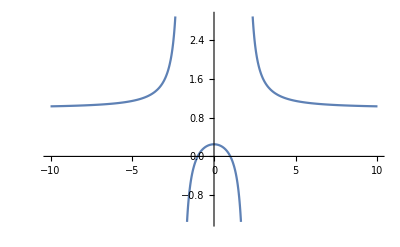

```mathematica
Plot[f[x], {x, -10, 10}]
```

```mathematica
nicle = Solve[f[x] == 0, x]
```

{{x→-1},{x→1}}

```mathematica
poli =Solve[Denominator[f[x]] == 0, x]
```

{{x→-2},{x→2}}

```mathematica
Limit[f[x], x->Infinity]
```

1

```mathematica
Limit[f[x], x-> -Infinity]
```

1

```mathematica
Solve[D[f[x], x] == 0, x]
```

{{x→0}}

```mathematica
Solve[D[f[x], {x, 2}] == 0, x]
```

{{x→-(2 ⅈ)/(√3)},{x→(2 ⅈ)/(√3)}}

```mathematica
Reduce[D[f[x], {x, 2}] > 0, x, Reals]
```

x<-2||x>2

```mathematica
f[x] == 0
```

(-1+x^2)/(-4+x^2)==0

```mathematica
D[f[x], {x, 2}]
```

-(8 x^2)/((-4+x^2)^2)+2/(-4+x^2)+(-1+x^2) ((8 x^2)/((-4+x^2)^3)-2/((-4+x^2)^2))

### Naloga 8

```mathematica
ClearAll[izraz, x]
izraz = x^4 + x^3 - x
```

-x+x^3+x^4

```mathematica
resitve = x/.Solve[izraz == 0 && x > 0, x]
Power[resitve, 2] // N
```

{Root[-1+#1^2+#1^3&,1]}

{0.56984}

### Naloga 9

```mathematica
enacba1 = 3x^2 - 5y^2 == 5
enacba2 = 2x^2 + 3y^2 == 59
```

3 x^2-5 y^2==5

2 x^2+3 y^2==59

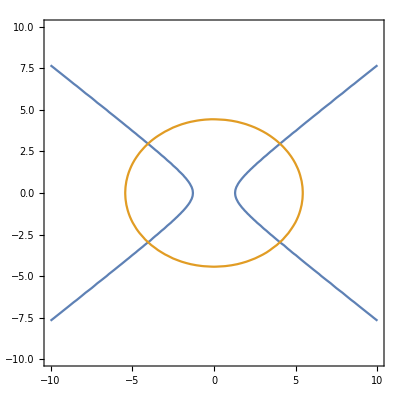

```mathematica
ContourPlot[{3x^2 - 5y^2 == 5,2x^2 + 3y^2 == 59} , {x, -10, 10}, {y, -10, 10}]
```

```mathematica
resitev =Solve[enacba1 && enacba2 && x > 0 && y > 0, {x, y}]
x0 = x /. resitev[[1]]
y0 =y /. resitev[[1]]
```

{{x→√(310/19),y→√(167/19)}}

√(310/19)

√(167/19)

```mathematica
k1 =D[y/.Solve[enacba1 && x >= 0 && y >= 0, y, Reals]//First, x] /. x-> x0
k2 =D[y/.Solve[enacba2 && x >= 0 && y >= 0, y, Reals]//First, x] /. x-> x0
Abs[ArcTan[k1] - ArcTan[k2]]/Degree//N
```

3 √(62/835)

-(2 √(310/167))/3

81.5141